# Toy Model

Assume a toy model that can be represented by simple data with following assumptions.

each data starts from 0 brightness. f(0)=0

data starts to climb to the maximum linearly from the start of the climb point

if data reaches to its maximum it will stay there

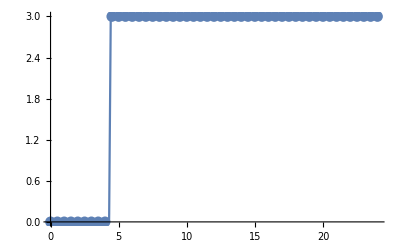

0.697674

```mathematica
Clear["Global`*"]

startPoint=4.3;
maximum = 3;
slope =25;

f[x_]=If[x<startPoint,0,If[x>(maximum/slope+startPoint),maximum,slope*(x-startPoint)]];
fig1=Plot[f[x], {x, 0, 24}, PlotRange -> Full];
m=Table[{x,f[x]},{x,0,24,0.5}];
fig2=ListPlot[m];
Show[fig1,fig2]
N[maximum/startPoint]
```